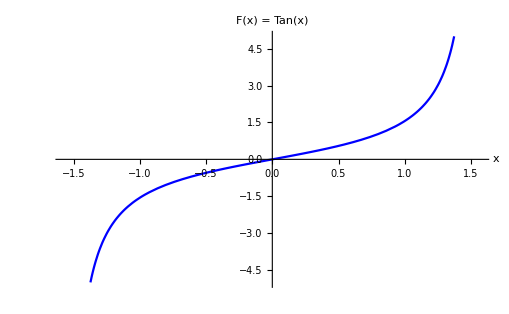

```mathematica
Other Types of Trigonometric Functions
Plot[Tan[x],{x,(- Pi)/2, Pi/2}, PlotRange->{-5,5}, AxesLabel->Automatic,PlotLabel-> "F(x) = Tan(x)", LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0],Bold},PlotStyle ->RGBColor[0.000106813, 0.00175479, 0.998215]]
```

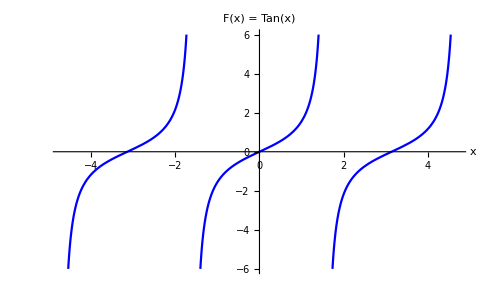

```mathematica
Plot[Tan[x],{x,(-3 Pi)/2, (3Pi)/2}, PlotRange->{-6,6}, AxesLabel->Automatic,PlotLabel-> "F(x) = Tan(x)", LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0],Bold},PlotStyle ->RGBColor[0.000106813, 0.00175479, 0.998215]]
```

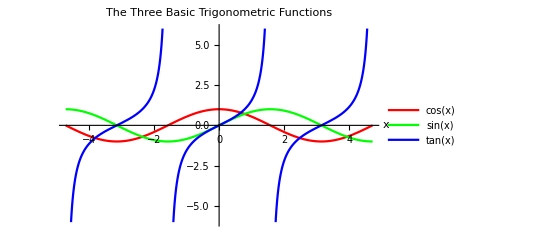

```mathematica
Plot[{Cos[x],Sin[x],Tan[x]},{x,(-3 Pi)/2, (3Pi)/2}, PlotRange->{-6,6}, AxesLabel->Automatic,PlotLabel-> "The Three Basic Trigonometric Functions", PlotLegends -> "Expressions" ,LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0],Bold},PlotStyle ->{Red,Green,RGBColor[0.000106813, 0.00175479, 0.998215]}]
```

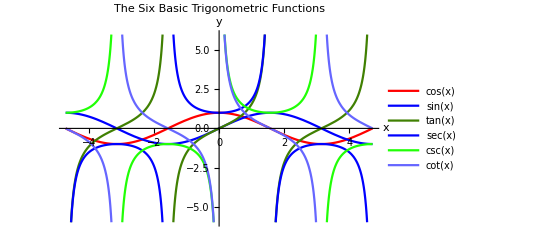

```mathematica
Plot[{Cos[x],Sin[x],Tan[x], Sec[x],Csc[x],Cot[x]},{x,(-3 Pi)/2, (3Pi)/2}, PlotRange->{-6,6}, AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel-> "The Six Basic Trigonometric Functions", PlotLegends -> "Expressions" ,LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0],Bold},PlotStyle ->{Red,Blue,RGBColor[0.25098, 0.501946, 0.00895705],RGBColor[0.000106813, 0.00175479, 0.998215],RGBColor[0.13135, 0.99968, 0.023621],RGBColor[0.4, 0.400107, 0.998566]}]
```

## Transformation of A tan(Bx) Functions

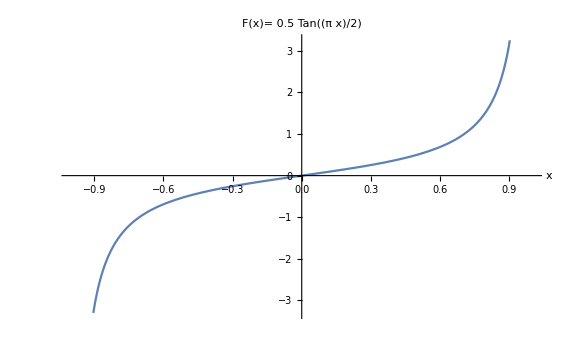

```mathematica
Plot[ 0.5 Tan[(Pi x)/2],{x,-1, 1},PlotRange->Automatic,AxesLabel->Automatic,PlotLabel -> "F(x)= 0.5 Tan((π x)/2)",LabelStyle ->{FontFamily->"Times New Roman",12,GrayLevel[0],Bold}]
```

```mathematica
Graphing One Period of a Shifted Tangent Function
```

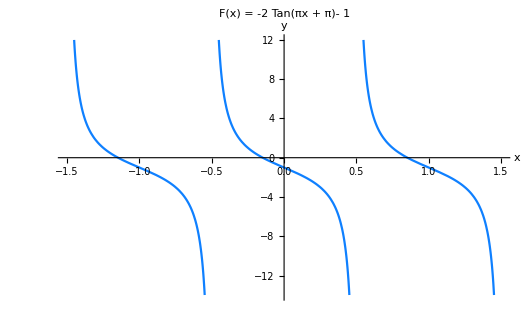

```mathematica
Plot[-2 Tan[Pi x + Pi]- 1,{x, -1.5, 1.5},PlotRange->Automatic,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->"F(x) = -2 Tan(πx + π)- 1",LabelStyle->{"Times New Roman", 12,GrayLevel[0], Bold},PlotStyle -> RGBColor[0.0595102, 0.50193, 0.998459]]
```

#### Comparison between the original function and the transform function

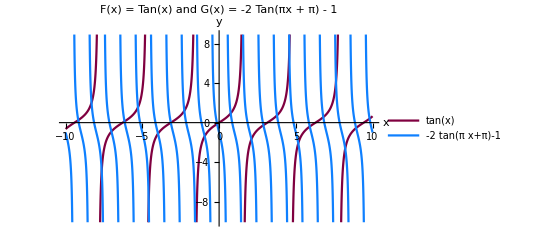

```mathematica
Plot[{Tan[x],-2 Tan[Pi x + Pi]-1},{x, -10, 10},PlotRange->Automatic,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->"F(x) = Tan(x) and G(x) = -2 Tan(πx + π) - 1",PlotLegends -> "Expressions", LabelStyle->{"Times New Roman", 12,GrayLevel[0], Bold},PlotStyle ->{RGBColor[0.501961, 0, 0.25098], RGBColor[0.0595102, 0.50193, 0.998459]}]
```

## Identifying the Graph of a Stretched Tangent

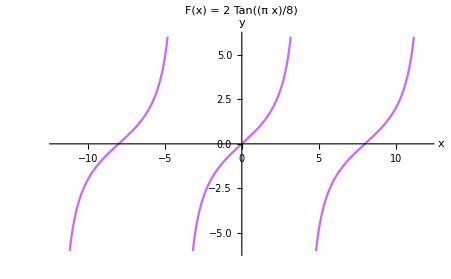

```mathematica
Plot[2 Tan[(Pi  x)/8],{x, -12, 12},  PlotRange -> {-6,6}, AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->"F(x) = 2 Tan((π x)/8)", LabelStyle->{"Times New Roman", 12, GrayLevel[0], Bold}, PlotStyle->RGBColor[0.8, 0.400076, 0.999023]]
```

## Analyzing the Graphs of y = sec x and y = csc x

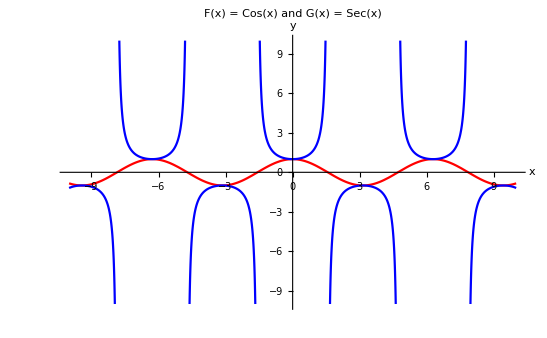

```mathematica
Plot[{Cos[x],Sec[x]},{x, -10, 10}, PlotRange->{-10,10},AxesLabel->{HoldForm[x],HoldForm[y]}, PlotLabel->"F(x) = Cos(x) and G(x) = Sec(x)",
LabelStyle->{"Times New Roman", 12, GrayLevel[0]},PlotStyle ->{Red, Blue}]
```

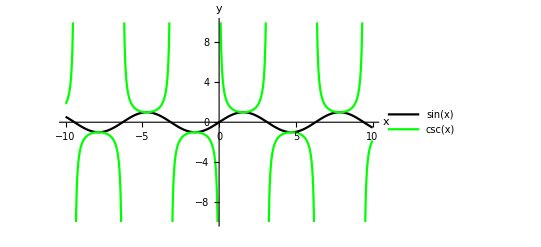

```mathematica
Plot[{Sin[x],Csc[x]},{x, -10, 10}, PlotRange->{-10,10},AxesLabel->{HoldForm[x],HoldForm[y]},
LabelStyle->{"Times New Roman", 12, GrayLevel[0]},PlotStyle ->{Black,Green}, PlotLegends -> "Expressions"]
```

## Graphing a Variation of the Secant Function

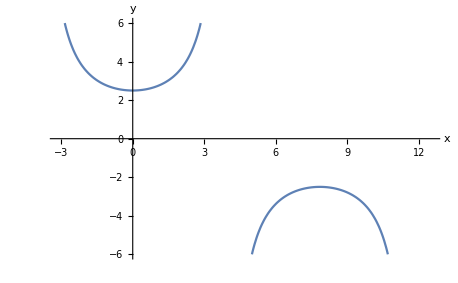

```mathematica
Plot[2.5 Sec[0.4x],{x,-Pi, 4Pi}, PlotRange->{-6,6},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0], Bold}]
```

## Graphing a Variation of the Secant Function

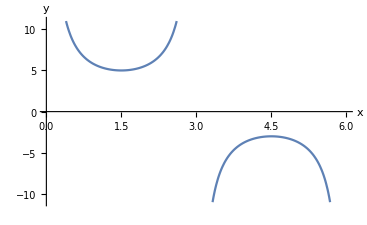

```mathematica
Plot[ 4 Sec[(Pi x)/3-Pi/2]+1,{x,0,6}, PlotRange->{-11,11}, AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold}]
```

## Graphing a Variation of the Cosecant Function

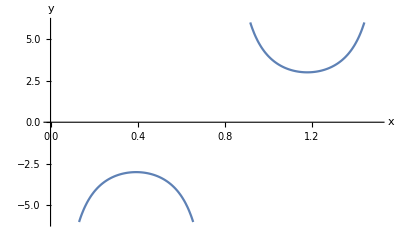

```mathematica
Plot[-3 Csc[4x],{x, 0,1.5},PlotRange->{-6,6},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0], Bold}]
```

## Graphing a Vertically Stretched, Horizontally Compressed, and Vertically Shifted Cosecant

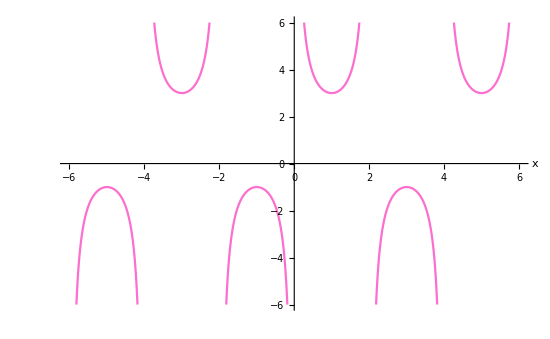

```mathematica
Plot[2 Csc[(Pi x)/2]+ 1, {x, -6, 6}, PlotRange->{-6,6}, AxesLabel->Automatic,LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->RGBColor[0.989014, 0.435737, 0.811749]]
```

## Graph of y = cot x

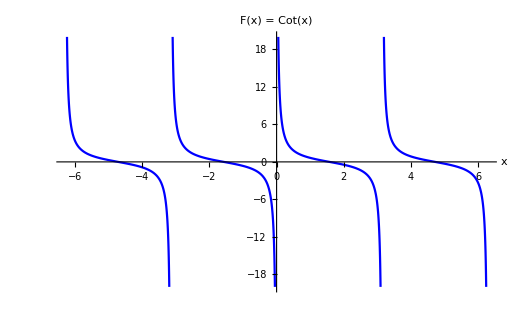

```mathematica
Plot[Cot[x],{x,-2 Pi, 2 Pi}, PlotRange->{-20,20}, AxesLabel->Automatic,PlotLabel-> "F(x) = Cot(x)", LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0],Bold},PlotStyle ->RGBColor[0.000106813, 0.00175479, 0.998215]]
```

## Graphing Variations of the Cotangent Function

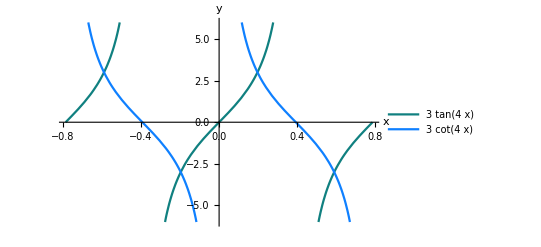

```mathematica
Plot[{3 Tan[4x], 3Cot[4 x]},{x, -Pi/4,Pi/4}, PlotRange->{-6,6},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle-> {"Times New Roman", 12,GrayLevel[0],Bold},PlotStyle -> {RGBColor[0.0641184, 0.501823, 0.501976],RGBColor[0.0595102, 0.50193, 0.998459]},PlotLegends->"Expressions"]
```

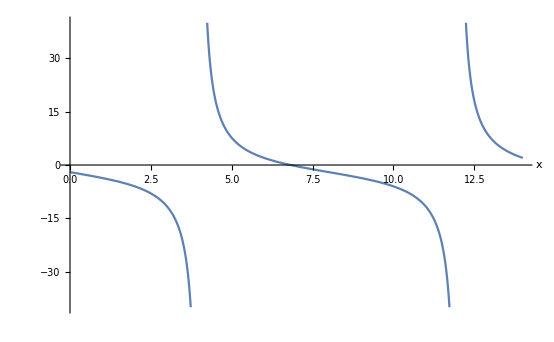

```mathematica
Plot[4 Cot[(Pi x)/8-Pi/2]-2,{x, 0, 14}, PlotRange->{-40,40},AxesLabel->Automatic,LabelStyle->{"Times New Roman", 12, GrayLevel[0], Bold}]
```